# Análisis de entropía

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Información de los paquetes cargados

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Cargar base de datos

```mathematica
database = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","DJI_DAX_MXX_NIKKEI_dataset.wdx"}]];
```

## Cálculo de entropía discreta (vale verga)

```mathematica
market = First[database];
```

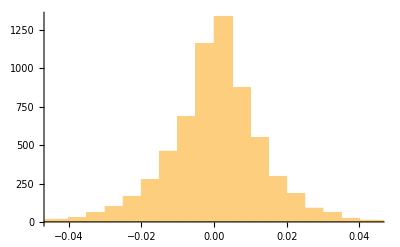

```mathematica
Histogram[market["Returns"]]
```

```mathematica
QuantilesForDiscretization[n_]:=Table[i/n,{i,1,n-1}];
DiscretizationIntervals[data_,n_]:=Block[{quantiles},
quantiles = Quantile[data,QuantilesForDiscretization[n]];
Partition[Join[{-∞},quantiles,{∞}],2,1]
];
DiscretizeWithEqualProbability[data_,n_]:=Block[{intervals,discreteStates, rules},
intervals = DiscretizationIntervals[data,n];
discreteStates = Range[Length[intervals]];
rules = MapThread[x_/;IntervalMemberQ[Interval[#1],x]->#2&,{intervals,discreteStates}];

data/. rules
];
```

```mathematica
N[Entropy[DiscretizeWithEqualProbability[market["Returns"],4]]]
```

1.38629

```mathematica
N[Entropy[DiscretizeWithEqualProbability[GroupReturnsByRun[market][1],10]]]
```

2.30258

```mathematica
N[Entropy[DiscretizeWithEqualProbability[GroupReturnsByRun[market][2],10]]]
```

2.30257

```mathematica
GroupReturnsByRun[market_]:=KeySort[GroupBy[Thread[{TrendDuration[market["Prices"]],market["TrendReturns"]}],First->Last]];
EntropyByRun[market_,n_,maxRun_ : 6]:=Block[{entropiesVsRunLength},
entropiesVsRunLength = Take[Map[N[Entropy[DiscretizeWithEqualProbability[#,n]]]&,GroupReturnsByRun[market]],maxRun];
Thread[{Normal[entropiesVsRunLength][[All,1]],Normal[entropiesVsRunLength][[All,2]]}]
];
```

```mathematica
EntropyByRun[market,100]
```

{{1,4.60474},{2,4.60345},{3,4.60416},{4,4.60517},{5,4.56997},{6,3.80666}}

```mathematica
Map[Length,GroupReturnsByRun[market]]
```

<|1→1637,2→844,3→397,4→200,5→112,6→45,7→21,8→8,9→3,10→1,11→2,12→3,13→1|>

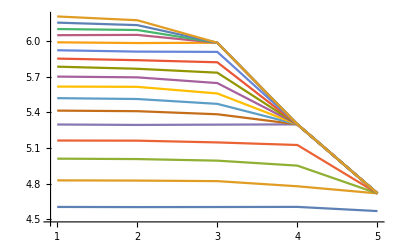

```mathematica
ListLinePlot[ProgressTable[EntropyByRun[market,partitions,5],{partitions,100,500,25}]]
```

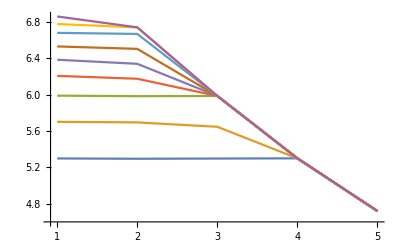

```mathematica
ListLinePlot[ProgressTable[EntropyByRun[market,partitions,5],{partitions,200,1000,100}]]
```

```mathematica
entropiesVsRunLength = Take[Map[N[Entropy[DiscretizeWithEqualProbability[#,4]]]&,GroupReturnsByRun[market]],6];
```

```mathematica
Thread[{Normal[entropiesVsRunLength][[All,1]],Normal[entropiesVsRunLength][[All,2]]}]
```

{{1,1.38629},{2,1.38629},{3,1.38628},{4,1.38629},{5,1.38629},{6,1.38556}}

Para los trends de longitud 1

```mathematica
entropies = Table[{partitions,Last[First[EntropyByRun[market,partitions]]]},{partitions,10,300,10}];
```

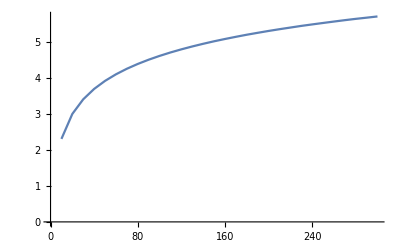

```mathematica
ListLinePlot[entropies]
```

```mathematica
entropies
```

{{10,2.30258},{20,2.99572},{30,3.40116},{40,3.68886},{50,3.91193},{60,4.09421},{70,4.24828},{80,4.38155},{90,4.49958},{100,4.60474},{110,4.70024},{120,4.78687},{130,4.86672},{140,4.94086},{150,5.01029},{160,5.07399},{170,5.13453},{180,5.19245},{190,5.24542},{200,5.29722},{210,5.34557},{220,5.39141},{230,5.43709},{240,5.47843},{250,5.51856},{260,5.558},{270,5.5967},{280,5.63281},{290,5.6658},{300,5.69963}}

## Calculo de entropía continua

```mathematica
GroupReturnsByRun[market_]:=KeySort[GroupBy[Thread[{TrendDuration[market["Prices"]],market["TrendReturns"]}],First->Last]];
ContinuousEntropy[data_]:=Block[{dist},
 dist= SmoothKernelDistribution[data];
-Quiet@NIntegrate[PDF[dist,x]*Log[PDF[dist,x]/PDF[UniformDistribution[{Min[data],Max[data]}],x]],{x,Min[data],Max[data]},Method->{"MonteCarlo","MaxPoints"->3000000},WorkingPrecision->20,MinRecursion->4,MaxRecursion->200]
];
ContinuousEntropySafe[data_]:=Mean@Table[ContinuousEntropy[data],4];
ContinousEntropyByRun[market_,maxRun_ : 6]:=Block[{entropiesVsRunLength},
entropiesVsRunLength = ProgressMap[ContinuousEntropySafe,Take[GroupReturnsByRun[market],maxRun]];
Thread[{Normal[entropiesVsRunLength][[All,1]],Normal[entropiesVsRunLength][[All,2]]}]
];
```

```mathematica
Clear[ContinousEntropyByRun]
```

```mathematica
ContinuousEntropySafe[data[1]]
```

-0.939573619945054

```mathematica
data = GroupReturnsByRun[market];
```

```mathematica
entropiesMarkets = ProgressMap[ContinousEntropyByRun[#,4]&,database];
```

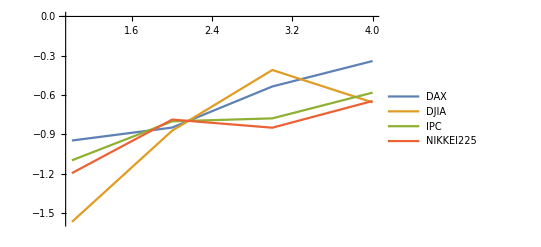

```mathematica
ListLinePlot[entropiesMarkets,PlotRange->All,PlotLegends->database[[All,"Name"]]]
```